Some Basic Equations (See: X-Ray Data Booklet)

```mathematica
nForm[num_]:=Print[NumberForm[N[num,8],{10,7},NumberFormat->(SequenceForm[#1,"D",#3]&),ExponentFunction->(#&)]]
```

```mathematica
wx[yIn_]:=(3/(5Pi))NIntegrate[BesselK[5/3,yi],{yi,yIn,Infinity}]
```

```mathematica
dwx[yIn_]:=-(3/(5 Pi))BesselK[5/3,yIn]
```

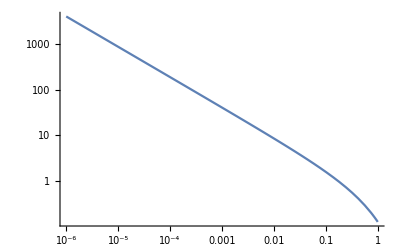

```mathematica
LogLogPlot[wx[z],{z,10^-6,1}]
```

```mathematica
swx[yIn_]:=(3/(5 Pi))yIn^(2/3) NIntegrate[BesselK[5/3,yi],{yi,yIn,Infinity}]
```

```mathematica
dswx[yIn_]:=(3/(5 Pi)) yIn^(2/3) (-BesselK[5/3,yIn]+(2/(3yIn)) NIntegrate[BesselK[5/3,yi],{yi,yIn,Infinity}])
```

```mathematica
dswxLog[yIn_]:=dswx[yIn]yIn Log[10]
```

```mathematica
nForm[Map[swx,PowerRange[10^-7,10^-2,10]]]
```

{4.1052219D-1,4.1049501D-1,4.1036886D-1,4.0978334D-1,4.0706563D-1,3.9445841D-1}

```mathematica
nForm[Map[dswxLog,PowerRange[10^-7,10^-2,10]]]
```

{-1.1456421D-5,-5.3175995D-5,-2.4682107D-4,-1.1456386D-3,-5.3172381D-3,-2.4646674D-2}

```mathematica
nForm[Map[swx,Range[0.01,0.1,0.01]]]
```

{3.9445841D-1,3.8503667D-1,3.7715318D-1,3.7013587D-1,3.6370582D-1,3.5771314D-1,3.5206552D-1,3.4670102D-1,3.4157550D-1,3.3665612D-1}

```mathematica
nForm[Map[dswx,Range[0.01,0.1,0.01]]]
```

{-1.0703915D0,-8.4772113D-1,-7.3863972D-1,-6.6916168D-1,-6.1924820D-1,-5.8078618D-1,-5.4975032D-1,-5.2387509D-1,-5.0176995D-1,-4.8252543D-1}

```mathematica
nForm[Map[swx,Range[0.1,1,0.02]]]
```

{3.3665612D-1,3.2733982D-1,3.1860491D-1,3.1035234D-1,3.0251133D-1,2.9502902D-1,2.8786450D-1,2.8098528D-1,2.7436495D-1,2.6798161D-1,2.6181686D-1,2.5585499D-1,2.5008243D-1,2.4448736D-1,2.3905935D-1,2.3378917D-1,2.2866855D-1,2.2369004D-1,2.1884691D-1,2.1413302D-1,2.0954277D-1,2.0507099D-1,2.0071291D-1,1.9646414D-1,1.9232056D-1,1.8827836D-1,1.8433395D-1,1.8048397D-1,1.7672528D-1,1.7305489D-1,1.6946999D-1,1.6596792D-1,1.6254615D-1,1.5920228D-1,1.5593402D-1,1.5273919D-1,1.4961572D-1,1.4656161D-1,1.4357497D-1,1.4065395D-1,1.3779681D-1,1.3500187D-1,1.3226751D-1,1.2959217D-1,1.2697435D-1,1.2441259D-1}

```mathematica
nForm[Map[dswx,Range[0.1,1,0.02]]]
```

{-4.8252543D-1,-4.5029908D-1,-4.2400202D-1,-4.0183669D-1,-3.8269981D-1,-3.6586975D-1,-3.5085095D-1,-3.3728967D-1,-3.2492535D-1,-3.1356101D-1,-3.0304439D-1,-2.9325558D-1,-2.8409857D-1,-2.7549540D-1,-2.6738195D-1,-2.5970488D-1,-2.5241938D-1,-2.4548744D-1,-2.3887657D-1,-2.3255877D-1,-2.2650975D-1,-2.2070831D-1,-2.1513581D-1,-2.0977581D-1,-2.0461371D-1,-1.9963648D-1,-1.9483244D-1,-1.9019109D-1,-1.8570296D-1,-1.8135944D-1,-1.7715270D-1,-1.7307560D-1,-1.6912160D-1,-1.6528469D-1,-1.6155934D-1,-1.5794043D-1,-1.5442323D-1,-1.5100336D-1,-1.4767671D-1,-1.4443949D-1,-1.4128812D-1,-1.3821929D-1,-1.3522985D-1,-1.3231687D-1,-1.2947759D-1,-1.2670939D-1}

```mathematica
ewx[yIn_]:=(3/(5 Pi))Exp[yIn] Sqrt[yIn]NIntegrate[BesselK[5/3,yi],{yi,yIn,Infinity}]
```

```mathematica
dewx[yIn_]:=(3/(5 Pi))Exp[yIn]Sqrt[yIn](-BesselK[5/3,yIn]+(1+1/(2yIn))NIntegrate[BesselK[5/3,yi],{yi,yIn,Infinity}])
```

```mathematica
nForm[Map[ewx,Range[1,3,0.05]]]
```

{3.3818849D-1,3.3516487D-1,3.3233973D-1,3.2969287D-1,3.2720686D-1,3.2486656D-1,3.2265876D-1,3.2057185D-1,3.1859560D-1,3.1672095D-1,3.1493984D-1,3.1324506D-1,3.1163017D-1,3.1008936D-1,3.0861740D-1,3.0720955D-1,3.0586152D-1,3.0456940D-1,3.0332963D-1,3.0213895D-1,3.0099437D-1,2.9989316D-1,2.9883280D-1,2.9781096D-1,2.9682551D-1,2.9587445D-1,2.9495594D-1,2.9406829D-1,2.9320991D-1,2.9237932D-1,2.9157514D-1,2.9079610D-1,2.9004099D-1,2.8930869D-1,2.8859815D-1,2.8790838D-1,2.8723846D-1,2.8658751D-1,2.8595472D-1,2.8533932D-1,2.8474057D-1}

```mathematica
nForm[Map[dewx,Range[1,3,0.05]]]
```

{-6.2608102D-2,-5.8415126D-2,-5.4657613D-2,-5.1274686D-2,-4.8216055D-2,-4.5439837D-2,-4.2910890D-2,-4.0599528D-2,-3.8480510D-2,-3.6532254D-2,-3.4736203D-2,-3.3076320D-2,-3.1538682D-2,-3.0111146D-2,-2.8783081D-2,-2.7545137D-2,-2.6389069D-2,-2.5307573D-2,-2.4294163D-2,-2.3343061D-2,-2.2449100D-2,-2.1607654D-2,-2.0814563D-2,-2.0066084D-2,-1.9358833D-2,-1.8689751D-2,-1.8056063D-2,-1.7455246D-2,-1.6885003D-2,-1.6343240D-2,-1.5828040D-2,-1.5337649D-2,-1.4870460D-2,-1.4424995D-2,-1.3999893D-2,-1.3593903D-2,-1.3205867D-2,-1.2834719D-2,-1.2479468D-2,-1.2139199D-2,-1.1813062D-2}

```mathematica
nForm[Map[ewx,Range[3,10,0.2]]]
```

{2.8474057D-1,2.8249896D-1,2.8047519D-1,2.7863827D-1,2.7696291D-1,2.7542827D-1,2.7401700D-1,2.7271453D-1,2.7150852D-1,2.7038847D-1,2.6934536D-1,2.6837140D-1,2.6745984D-1,2.6660478D-1,2.6580106D-1,2.6504414D-1,2.6432999D-1,2.6365504D-1,2.6301612D-1,2.6241038D-1,2.6183528D-1,2.6128852D-1,2.6076805D-1,2.6027198D-1,2.5979864D-1,2.5934648D-1,2.5891409D-1,2.5850020D-1,2.5810363D-1,2.5772332D-1,2.5735827D-1,2.5700758D-1,2.5667040D-1,2.5634598D-1,2.5603358D-1,2.5573256D-1}

```mathematica
nForm[Map[dewx,Range[3,10,0.2]]]
```

{-1.1813062D-2,-1.0634850D-2,-9.6285326D-3,-8.7616650D-3,-8.0092079D-3,-7.3515685D-3,-6.7732249D-3,-6.2617422D-3,-5.8070577D-3,-5.4009530D-3,-5.0366595D-3,-4.7085591D-3,-4.4119559D-3,-4.1428985D-3,-3.8980419D-3,-3.6745382D-3,-3.4699500D-3,-3.2821809D-3,-3.1094194D-3,-2.9500932D-3,-2.8028323D-3,-2.6664382D-3,-2.5398586D-3,-2.4221666D-3,-2.3125427D-3,-2.2102605D-3,-2.1146740D-3,-2.0252072D-3,-1.9413450D-3,-1.8626257D-3,-1.7886346D-3,-1.7189981D-3,-1.6533789D-3,-1.5914720D-3,-1.5330010D-3,-1.4777149D-3}

```mathematica
nForm[Map[ewx,Range[10,40,1]]]
```

{2.5573256D-1,2.5437801D-1,2.5323167D-1,2.5224879D-1,2.5139659D-1,2.5065056D-1,2.4999195D-1,2.4940622D-1,2.4888186D-1,2.4840969D-1,2.4798226D-1,2.4759351D-1,2.4723838D-1,2.4691270D-1,2.4661294D-1,2.4633612D-1,2.4607970D-1,2.4584150D-1,2.4561965D-1,2.4541251D-1,2.4521867D-1,2.4503689D-1,2.4486607D-1,2.4470524D-1,2.4455357D-1,2.4441028D-1,2.4427470D-1,2.4414622D-1,2.4402430D-1,2.4390845D-1,2.4379822D-1}

```mathematica
nForm[Map[dewx,Range[10,40,1]]]
```

{-1.4777149D-3,-1.2417257D-3,-1.0583022D-3,-9.1286524D-4,-7.9557438D-4,-6.9958881D-4,-6.2003118D-4,-5.5334694D-4,-4.9689529D-4,-4.4868069D-4,-4.0717218D-4,-3.7117922D-4,-3.3976460D-4,-3.1218231D-4,-2.8783255D-4,-2.6622856D-4,-2.4697197D-4,-2.2973422D-4,-2.1424234D-4,-2.0026803D-4,-1.8761915D-4,-1.7613308D-4,-1.6567140D-4,-1.5611572D-4,-1.4736428D-4,-1.3932922D-4,-1.3193437D-4,-1.2511345D-4,-1.1880850D-4,-1.1296875D-4,-1.0754950D-4}